# Using the SACNA package - Replicator model of Hochberg and Ribó

The purpose of this document is to give a short tutorial for the SACNA package. 
Let’s start by bringing the package functions to this notebook.

```mathematica
Quiet[ClearAll["Global`*"]];
 Quiet[Remove["Global`*"]];
SetDirectory[NotebookDirectory[]];
Quiet[Get["../SACNA.wl"]]
```

Now let’s input the reactions and rates lists of this model. If we input the rates list as an empty list, SACNA will assign rates by default. Reactions must be in terms of D-species, L-species, Z-species (achiral species), and the empty specie N1. This sample show us that we can find a solution with some Routh-Hurwitz condition, but others may

```mathematica
reactions = {"Z1+D1+D2->2D1+D2","2D1+D2->Z1+D1+D2","Z1+D1+D2->D1+2D2","D1+2D2->Z1+D1+D2","D1->N1","D2->N1","N1->Z1","Z1->N1"};
rates={};
```

Now we can run the semialgebraic analysis of the model by using the RunSemiAlgebraicAnalysis function. The first parameter corresponds to the reactions’ list, the second parameter corresponds to the rates’ list, and the last parameter corresponds to time in seconds (the Collins’ algorithm may take so much time to find a solution). The function will ask for the Routh-Hurwitz condition number. Considering the first and last numbers will be faster, because this conditions are shorter than the others.  We will be choose the first condition.

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

False

Since the algorithm found that this condition cannot be satisfied, let’s try with the second Routh-Hurwitz condition.

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

D1>0&&D2>0&&k1>0&&k2>0&&k3>0&&k4>0&&k5>(D2^2 k1 k4)/k3&&k6==(D1^2 D2 k2 k3-D1 D2^2 k1 k4+D1 k3 k5)/(D2 k1)&&k7>(2 D1^2 D2 k2 k3-2 D1 D2^2 k1 k4+2 D1 k1 k5+2 D1 k3 k5)/k1&&k8==(-2 D1^2 D2^2 k2 k3+2 D1 D2^3 k1 k4-2 D1 D2 k1 k5-2 D1 D2 k3 k5+D2 k1 k7)/(D1 D2 k2+k5)&&Z1==(2 D1^2 D2 k2+2 D1 D2^2 k4+k7)/(2 D1 D2 k1+2 D1 D2 k3+k8)

The algorithm found a solution. Let’s find some particular solutions by using the FindInstance command.  Note that the solution doesn’t contain an expression for the L-species. It’s because we are assuming the racemic condition.

```mathematica
numberOfSamples=10; (*feel free to change*)
samplesList=FindInstance[cadSolutions,DeleteCases[DeleteDuplicates@Cases[cadSolutions,_Symbol,Infinity], Alternatives@@{GreaterEqual,Greater,Less,LessEqual}],numberOfSamples];
sampleNumber=7;   (*feel free to change*)
samplesList[[sampleNumber]]
```

{D1→663,D2→89,k1→28,k2→23,k3→54,k4→64,k5→262876,k6→24294828129/1246,k7→3819263381,k8→180136/1620037,Z1→1620037/2492}

Now we are ready to using the SACNA’s system simulator with the  ReactionSystemSimulator function

Species Concentrations Graphic

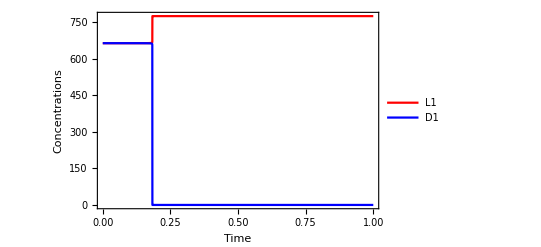

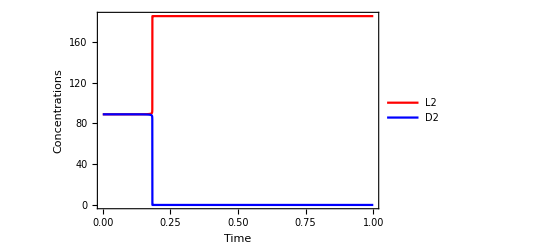

```mathematica
simulationTimeMin=0; 
simulationTimeMax=1; (*feel free to change*)
graficss=ReactionSystemSimulator[reactions,rates, samplesList[[sampleNumber]],0.00001,t,simulationTimeMin,simulationTimeMax];
```

SACNA also allows to export a simulation results to ChemKinLator simulator files with the function ExportToChemKinLator.

```mathematica
content=ExportToChemKinLator[reactions,rates, samplesList[[sampleNumber]],1/1000000000000000,1/1000000000000000,0,simulationTimeMax,1000];
```

Export::chtype: First argument $Canceled is not a valid file specification.

The user would like to know which rate constant corresponds to some reactions. It can be done with the function GetReactionsAndRates.

```mathematica
GetReactionsAndRates[reactions,rates] //MatrixForm
```

(D1+D2+Z1->2D1+D2 | k1
2D1+D2->D1+D2+Z1 | k2
D1+D2+Z1->D1+2D2 | k3
D1+2D2->D1+D2+Z1 | k4
D1->N1 | k5
D2->N1 | k6
N1->Z1 | k7
Z1->N1 | k8
L1+L2+Z1->2L1+L2 | k1
2L1+L2->L1+L2+Z1 | k2
L1+L2+Z1->L1+2L2 | k3
L1+2L2->L1+L2+Z1 | k4
L1->N1 | k5
L2->N1 | k6)